```mathematica
z = PauliMatrix[3]
x = PauliMatrix[1]
I1 = IdentityMatrix[2]
```

{{1,0},{0,-1}}

{{0,1},{1,0}}

{{1,0},{0,1}}

```mathematica
H=-2m (KroneckerProduct[z,I1]+KroneckerProduct[I1,z]) - KroneckerProduct[z,z] - Δ(KroneckerProduct[x,I1]+KroneckerProduct[I1,x]) //MatrixForm
```

(-1-4 m | -Δ | -Δ | 0
-Δ | 1 | 0 | -Δ
-Δ | 0 | 1 | -Δ
0 | -Δ | -Δ | -1+4 m)

```mathematica
eg0 = Eigenvalues[H]/.{ Δ->0}
```

```mathematica
Eigenvalues[({{-1-4 m, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1+4 m}})]
```

{1,1,-1-4 m,-1+4 m}

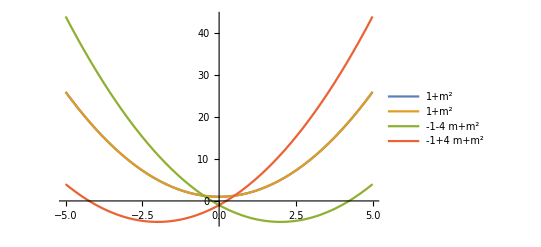

```mathematica
Plot[Evaluate[Normal[{1,1,-1-4 m,-1+4 m}+m^2]],{m, -5, 5}, PlotLegends->"Expressions"]
```

```mathematica
eg6 = Eigenvalues[H]/.{ Δ->0.1}
```

```mathematica
Eigenvalues[({{-1-4 m, -0.1, -0.1, 0}, {-0.1, 1, 0, -0.1}, {-0.1, 0, 1, -0.1}, {0, -0.1, -0.1, -1+4 m}})]
```

{Root[0.065-1.73472×10^-18 m-1. m^2+(1.73472×10^-18 m+2. m^2) #1+(-0.1275-1. m^2) #1^2+0.0625 #1^4&,1],Root[0.065-1.73472×10^-18 m-1. m^2+(1.73472×10^-18 m+2. m^2) #1+(-0.1275-1. m^2) #1^2+0.0625 #1^4&,2],Root[0.065-1.73472×10^-18 m-1. m^2+(1.73472×10^-18 m+2. m^2) #1+(-0.1275-1. m^2) #1^2+0.0625 #1^4&,3],Root[0.065-1.73472×10^-18 m-1. m^2+(1.73472×10^-18 m+2. m^2) #1+(-0.1275-1. m^2) #1^2+0.0625 #1^4&,4]}

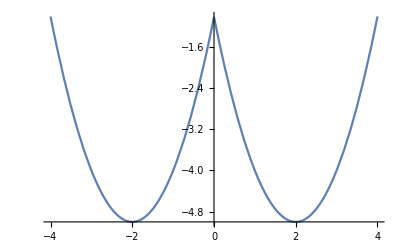

```mathematica
Plot[Evaluate[Normal[{Root[0.065-1.734723475976807*^-18 m-1. m^2+(1.734723475976807*^-18 m+2. m^2) #1+(-0.1275-1. m^2) #1^2+0.0625 #1^4&,1]}+m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
eg6 = Eigenvalues[H]/.{ Δ->0.3}
```

```mathematica
Eigenvalues[({{-1-4 m, -0.3, -0.3, 0}, {-0.3, 1, 0, -0.3}, {-0.3, 0, 1, -0.3}, {0, -0.3, -0.3, -1+4 m}})]
```

{Root[0.085-2.08167×10^-17 m-1. m^2+(2.08167×10^-17 m+2. m^2) #1+(-0.1475-1. m^2) #1^2+0.0625 #1^4&,1],Root[0.085-2.08167×10^-17 m-1. m^2+(2.08167×10^-17 m+2. m^2) #1+(-0.1475-1. m^2) #1^2+0.0625 #1^4&,2],Root[0.085-2.08167×10^-17 m-1. m^2+(2.08167×10^-17 m+2. m^2) #1+(-0.1475-1. m^2) #1^2+0.0625 #1^4&,3],Root[0.085-2.08167×10^-17 m-1. m^2+(2.08167×10^-17 m+2. m^2) #1+(-0.1475-1. m^2) #1^2+0.0625 #1^4&,4]}

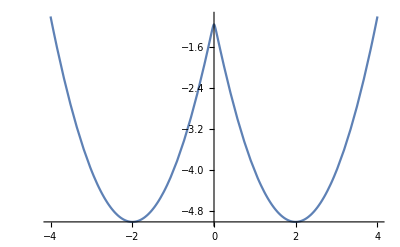

```mathematica
Plot[Evaluate[Normal[{Root[0.085-2.0816681711721685*^-17 m-1. m^2+(2.0816681711721685*^-17 m+2. m^2) #1+(-0.14750000000000002-1. m^2) #1^2+0.0625 #1^4&,1]}+m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
eg1 = Eigenvalues[H]/.{ Δ->-0.5}
```

```mathematica
Eigenvalues[({{-1-4 m, 0.5, 0.5, 0}, {0.5, 1, 0, 0.5}, {0.5, 0, 1, 0.5}, {0, 0.5, 0.5, -1+4 m}})]
```

{Root[0.125-1. m^2+2. m^2 #1+(-0.1875-1. m^2) #1^2+0.0625 #1^4&,1],Root[0.125-1. m^2+2. m^2 #1+(-0.1875-1. m^2) #1^2+0.0625 #1^4&,2],Root[0.125-1. m^2+2. m^2 #1+(-0.1875-1. m^2) #1^2+0.0625 #1^4&,3],Root[0.125-1. m^2+2. m^2 #1+(-0.1875-1. m^2) #1^2+0.0625 #1^4&,4]}

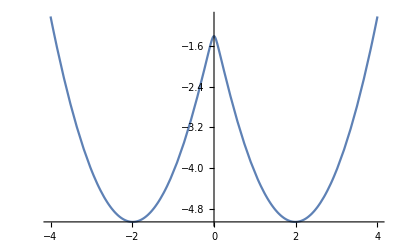

```mathematica
Plot[Evaluate[Normal[{Root[0.125-1. m^2+2. m^2 #1+(-0.1875-1. m^2) #1^2+0.0625 #1^4&,1]}+m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
eg1 = Eigenvalues[H]/.{ Δ->0.5}
```

```mathematica
Eigenvalues[({{-1-4 m, -0.5, -0.5, 0}, {-0.5, 1, 0, -0.5}, {-0.5, 0, 1, -0.5}, {0, -0.5, -0.5, -1+4 m}})]
```

{Root[0.125-1. m^2+2. m^2 #1+(-0.1875-1. m^2) #1^2+0.0625 #1^4&,1],Root[0.125-1. m^2+2. m^2 #1+(-0.1875-1. m^2) #1^2+0.0625 #1^4&,2],Root[0.125-1. m^2+2. m^2 #1+(-0.1875-1. m^2) #1^2+0.0625 #1^4&,3],Root[0.125-1. m^2+2. m^2 #1+(-0.1875-1. m^2) #1^2+0.0625 #1^4&,4]}

```mathematica
Plot[Evaluate[Normal[{Root[0.125-1. m^2+2. m^2 #1+(-0.1875-1. m^2) #1^2+0.0625 #1^4&,1]}+m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
eg2 = Eigenvalues[H]/.{ Δ->0.7}
```

```mathematica
Eigenvalues[({{-1-4 m, -0.7, -0.7, 0}, {-0.7, 1, 0, -0.7}, {-0.7, 0, 1, -0.7}, {0, -0.7, -0.7, -1+4 m}})]
```

{Root[0.185-1.38778×10^-17 m-1. m^2+(1.38778×10^-17 m+2. m^2) #1+(-0.2475-1. m^2) #1^2+0.0625 #1^4&,1],Root[0.185-1.38778×10^-17 m-1. m^2+(1.38778×10^-17 m+2. m^2) #1+(-0.2475-1. m^2) #1^2+0.0625 #1^4&,2],Root[0.185-1.38778×10^-17 m-1. m^2+(1.38778×10^-17 m+2. m^2) #1+(-0.2475-1. m^2) #1^2+0.0625 #1^4&,3],Root[0.185-1.38778×10^-17 m-1. m^2+(1.38778×10^-17 m+2. m^2) #1+(-0.2475-1. m^2) #1^2+0.0625 #1^4&,4]}

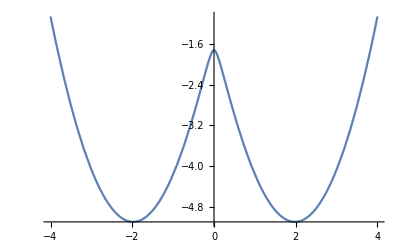

```mathematica
Plot[Evaluate[Normal[{Root[0.185-1.3877787807814457*^-17 m-1. m^2+(1.3877787807814457*^-17 m+2. m^2) #1+(-0.2475-1. m^2) #1^2+0.0625 #1^4&,1]}+m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
eg2 = Eigenvalues[H]/.{ Δ->1}
```

```mathematica
Eigenvalues[({{-1-4 m, -1, -1, 0}, {-1, 1, 0, -1}, {-1, 0, 1, -1}, {0, -1, -1, -1+4 m}})]
```

{1,Root[-5+16 m^2+(-5-16 m^2) #1+#1^2+#1^3&,1],Root[-5+16 m^2+(-5-16 m^2) #1+#1^2+#1^3&,2],Root[-5+16 m^2+(-5-16 m^2) #1+#1^2+#1^3&,3]}

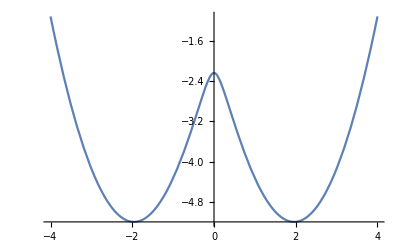

```mathematica
Plot[Evaluate[Normal[{Root[-5+16 m^2+(-5-16 m^2) #1+#1^2+#1^3&,1]}+m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
eg2 = Eigenvalues[H]/.{ Δ->2}
```

```mathematica
Eigenvalues[({{-1-4 m, -2, -2, 0}, {-2, 1, 0, -2}, {-2, 0, 1, -2}, {0, -2, -2, -1+4 m}})]
```

{1,Root[-17+16 m^2+(-17-16 m^2) #1+#1^2+#1^3&,1],Root[-17+16 m^2+(-17-16 m^2) #1+#1^2+#1^3&,2],Root[-17+16 m^2+(-17-16 m^2) #1+#1^2+#1^3&,3]}

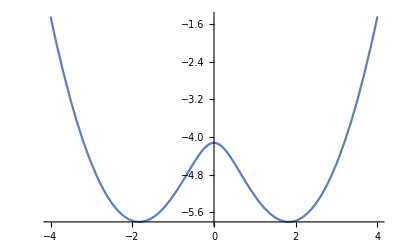

```mathematica
Plot[Evaluate[Normal[{Root[-17+16 m^2+(-17-16 m^2) #1+#1^2+#1^3&,1]}+m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
eg2 = Eigenvalues[H]/.{ Δ->3}
```

```mathematica
Eigenvalues[({{-1-4 m, -3, -3, 0}, {-3, 1, 0, -3}, {-3, 0, 1, -3}, {0, -3, -3, -1+4 m}})]
```

{1,Root[-37+16 m^2+(-37-16 m^2) #1+#1^2+#1^3&,1],Root[-37+16 m^2+(-37-16 m^2) #1+#1^2+#1^3&,2],Root[-37+16 m^2+(-37-16 m^2) #1+#1^2+#1^3&,3]}

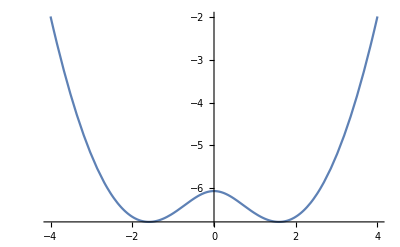

```mathematica
Plot[Evaluate[Normal[{Root[-37+16 m^2+(-37-16 m^2) #1+#1^2+#1^3&,1]}+m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
eg2 = Eigenvalues[H]/.{ Δ->4}
```

```mathematica
Eigenvalues[({{-1-4 m, -4, -4, 0}, {-4, 1, 0, -4}, {-4, 0, 1, -4}, {0, -4, -4, -1+4 m}})]
```

{1,Root[-65+16 m^2+(-65-16 m^2) #1+#1^2+#1^3&,1],Root[-65+16 m^2+(-65-16 m^2) #1+#1^2+#1^3&,2],Root[-65+16 m^2+(-65-16 m^2) #1+#1^2+#1^3&,3]}

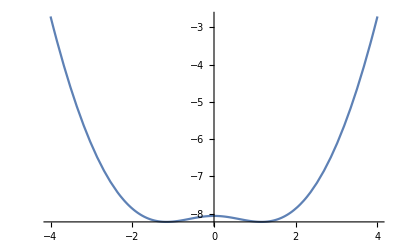

```mathematica
Plot[Evaluate[Normal[{Root[-65+16 m^2+(-65-16 m^2) #1+#1^2+#1^3&,1]}+m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
eg2 = Eigenvalues[H]/.{ Δ->4.5}
```

```mathematica
Eigenvalues[({{-1-4 m, -4.5, -4.5, 0}, {-4.5, 1, 0, -4.5}, {-4.5, 0, 1, -4.5}, {0, -4.5, -4.5, -1+4 m}})]
```

{Root[5.125-1. m^2+2. m^2 #1+(-5.1875-1. m^2) #1^2+0.0625 #1^4&,1],Root[5.125-1. m^2+2. m^2 #1+(-5.1875-1. m^2) #1^2+0.0625 #1^4&,2],Root[5.125-1. m^2+2. m^2 #1+(-5.1875-1. m^2) #1^2+0.0625 #1^4&,3],Root[5.125-1. m^2+2. m^2 #1+(-5.1875-1. m^2) #1^2+0.0625 #1^4&,4]}

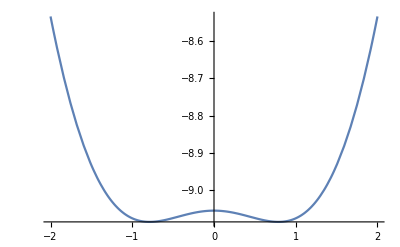

```mathematica
Plot[Evaluate[Normal[{Root[5.125-1. m^2+2. m^2 #1+(-5.1875-1. m^2) #1^2+0.0625 #1^4&,1]}+m^2]],{m, -2, 2}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[({{-1-4 m, -5, -5, 0}, {-5, 1, 0, -5}, {-5, 0, 1, -5}, {0, -5, -5, -1+4 m}})]
```

{1,Root[-101+16 m^2+(-101-16 m^2) #1+#1^2+#1^3&,1],Root[-101+16 m^2+(-101-16 m^2) #1+#1^2+#1^3&,2],Root[-101+16 m^2+(-101-16 m^2) #1+#1^2+#1^3&,3]}

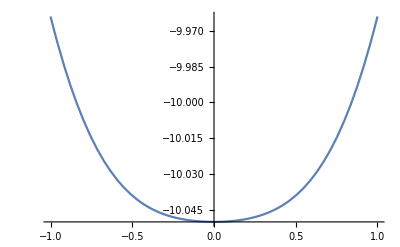

```mathematica
Plot[Evaluate[Normal[{Root[-101+16 m^2+(-101-16 m^2) #1+#1^2+#1^3&,1]}+m^2]],{m, -1, 1}, PlotLegends->"Expressions"]
```